## First define the genrator base

```mathematica
allGeneratorVariables=Sort[Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs4[k,"graph"]]]},
allGraphs4[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs4GeneratorAtomKeys}
],CompareSymbols];
```

```mathematica
repFullToGen=ToRules[
Reduce[
Table[
allGraphs4[k,"colofourgenerator"]==allGraphs4[k,"colofour"]
,
{k,allGraphs4GeneratorAtomKeys}
],
Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs4[k,"colofourgenerator"]=Simplify[allGraphs4[k,"colofour"]/.repFullToGen],
{k,Sort[Keys[allGraphs4]]}
],k];
```

```mathematica
allGraphs5[0,"colofournull"]
```

p1x2x3x4x5

## Now define the base basic data

```mathematica
Bases=Association[];
```

```mathematica
Bases["C"]=Association[];
```

```mathematica
Bases["C","Colofour"]="colofour";
```

```mathematica
Bases["E"]=Association[];
```

```mathematica
Bases["E","Colofour"]="colofourrealnull";
```

```mathematica
Bases["G"]=Association[];
```

```mathematica
Bases["G","Colofour"]="colofourgenerator";
```

```mathematica
Bases["F"]=Association[];
```

```mathematica
Bases["F","Colofour"]="colofournull";
```

```mathematica
allBases=Keys[Bases]
```

{C,E,G,F}

## Compute keys and variables

```mathematica
Table[Bases[base,"AtomKeys"]=Sort[Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,Bases[base,"Colofour"]]]]==1&],CompareSymbols[allGraphs4[#1,Bases[base,"Colofour"]],allGraphs4[#2,Bases[base,"Colofour"]]]&]
,{base,allBases}];
```

```mathematica
Table[Bases[base,"Variables"]=Table[allGraphs4[k,Bases[base,"Colofour"]],{k,Bases[base,"AtomKeys"]}]
,{base,allBases}];
```

```mathematica
BaseCoeff[key_,base_]:=Table[Coefficient[allGraphs4[key,Bases[base,"Colofour"]],var],{var,Bases[base,"Variables"]}]
```

```mathematica
BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix[base1_,base2_]:=Table[BaseCoeff[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases[base,"AtomKeys"],{base,allBases}]//Flatten//DeleteDuplicates//Length
```

55

## Checking some conversion matrix identities

```mathematica
ConversionMatrix["E","C"]==Transpose[ConversionMatrix["G","C"]]
```

True

```mathematica
ConversionMatrix["E","C"]==Inverse[ConversionMatrix["C","E"]]
```

True

```mathematica
ConversionMatrix["G","C"]==Transpose[Inverse[ConversionMatrix["C","E"]]]
```

True

```mathematica
Table[base->ConversionMatrix[base,base]==IdentityMatrix[42],{base,allBases}]
```

{C→False,E→False,G→False,F→False}

## Viewing come COnversion matrcxes

```mathematica
Table[Det[ConversionMatrix[base1,base2]],{base1,allBases},{base2,allBases}]
```

{{1,1,1,-1/96},{1,1,1,-1/96},{1,1,1,-1/96},{-96,-96,-96,1}}

```mathematica
Table[base1->Eigenvalues[ConversionMatrix[base1,base2]]//N,{base1,allBases},{base2,{"G"}}]
```

{{C→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{E→{0.+2.80588 ⅈ,0.-2.80588 ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,1.,0.+0.356394 ⅈ,0.-0.356394 ⅈ}},{G→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{F→{-6.,2.,2.,2.,2.,-1.,-1.,-1.,-1.,-1.,-1.,1.,1.,1.,1.}}}

```mathematica
Table[base1->Det[ConversionMatrix[base1,base2]],{base1,allBases},{base2,{"G"}}]
```

{{C→1},{E→1},{G→1},{F→-96}}

```mathematica
Tally[Table[Sort[Map[Length,allGraphs4[k,"vertexsets"]]],{k,allGraphs4AtomKeys}]]
```

{{{1,1,1,1},1},{{1,1,2},6},{{2,2},3},{{1,3},4},{{4},1}}

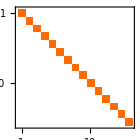
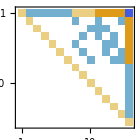
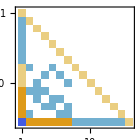
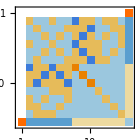
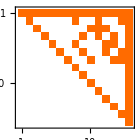
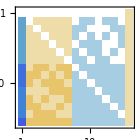
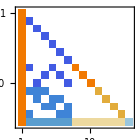
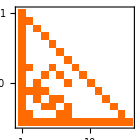
| C | E | G | F
C | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[base1,base2],ImageSize->140],{base1,allBases},{base2,allBases}],TableHeadings->{allBases, allBases},TableAlignments->{Center, Center}]
```

```mathematica
TableForm[Table[MatrixPlot[Inverse[ConversionMatrix[base1,base2]],ImageSize->140],{base1,allBases},{base2,allBases}],TableHeadings->{Reverse[allBases], Reverse[allBases]},TableAlignments->{Center, Center}]
```

| F | G | E | C
F | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics-
C | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ConversionMatrix["G","E"].ConversionMatrix["E","C"]==ConversionMatrix["G","C"]
```

True

```mathematica
labels=Table [With[
{k=Bases["E","AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]
```

{1→-Graphics-0,2→-Graphics-2,3→-Graphics-18,4→-Graphics-6,5→-Graphics-486,6→-Graphics-162,7→-Graphics-54,8→-Graphics-488,9→-Graphics-168,10→-Graphics-72,11→-Graphics-26,12→-Graphics-666,13→-Graphics-546,14→-Graphics-218,15→-Graphics-728}

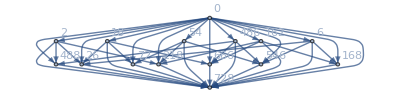
-Graphics-{15,45}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["E","C"]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

```mathematica
Keys[Bases]
```

{C,E,G,F}

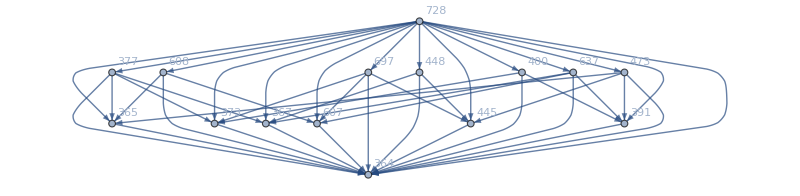
-Graphics-{15,45}

```mathematica
With[
{base1="G",base2="C"},
With[
{labels=Table [With[
{k=Bases[base2,"AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]},
With[{g=AdjacencyGraph[ConversionMatrix[base1,base2]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels,ImageSize->800]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
]
]
```

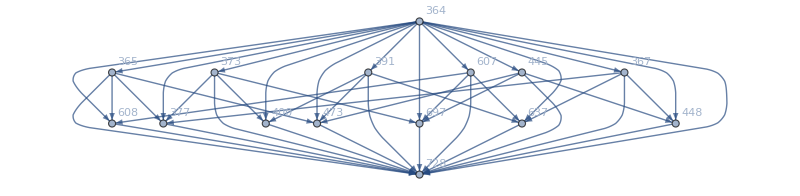
-Graphics-{15,45}

```mathematica
With[
{base1="E",base2="C"},
With[
{labels=Table [With[
{k=Bases[base2,"AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]},
With[{g=AdjacencyGraph[ConversionMatrix[base1,base2]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels,ImageSize->800]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
]
]
```

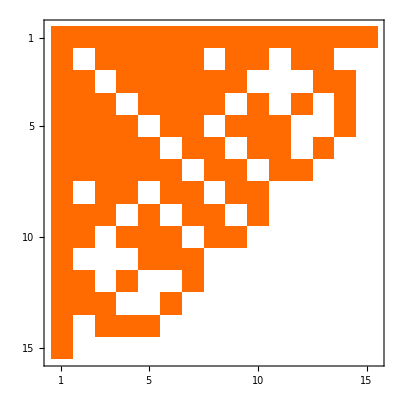

```mathematica
ConversionMatrix["F","C"]//MatrixPlot
```

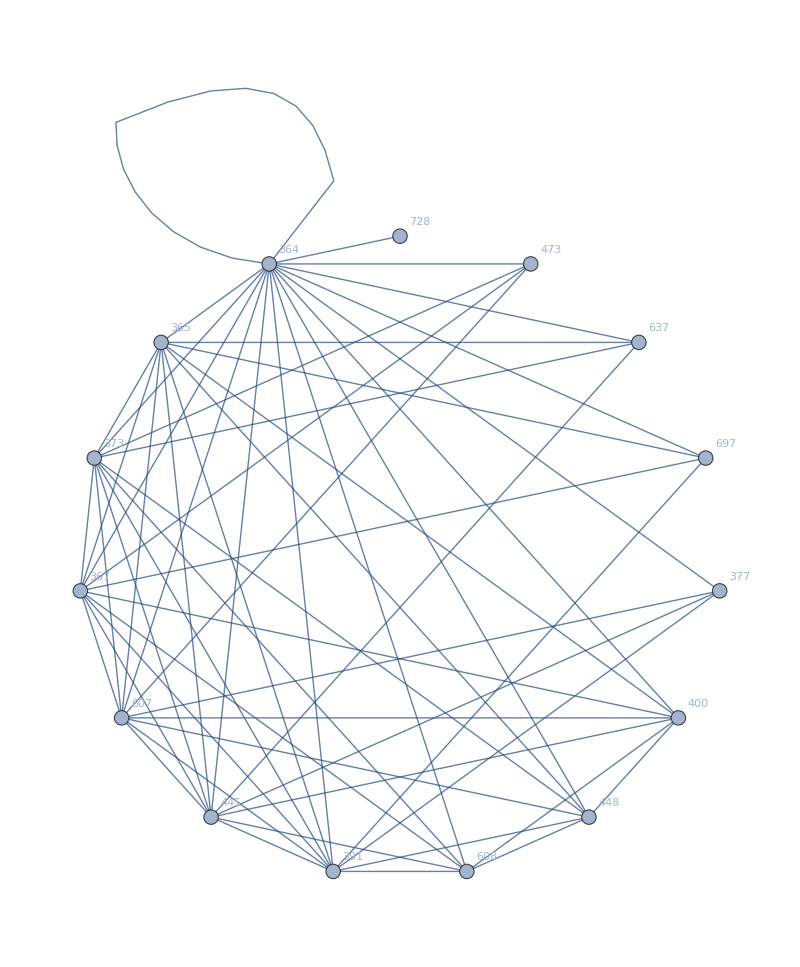
-Graphics-{15,57}

```mathematica
With[
{base1="F",base2="C"},
With[
{labels=Table [With[
{k=Bases[base2,"AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]},
With[{g=AdjacencyGraph[ConversionMatrix[base1,base2],VertexLabels->labels,ImageSize->800,GraphLayout->"CircularEmbedding"]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
]
]
```

```mathematica
Table[ShowGraph[allGraphs4,k],{k,Bases["G","AtomKeys"]}]
```

{-Graphics-364,-Graphics-363,-Graphics-355,-Graphics-361,-Graphics-121,-Graphics-283,-Graphics-337,-Graphics-120,-Graphics-280,-Graphics-328,-Graphics-351,-Graphics-31,-Graphics-91,-Graphics-255,-Graphics-0}

```mathematica
Table[ShowGraph[allGraphs4,k]->ShowGraph[allGraphs4,FindComplement[k,allGraphs4]],{k,Bases["G","AtomKeys"]}]
```

{-Graphics-364→-Graphics-0,-Graphics-363→-Graphics-1,-Graphics-355→-Graphics-9,-Graphics-361→-Graphics-3,-Graphics-121→-Graphics-243,-Graphics-283→-Graphics-81,-Graphics-337→-Graphics-27,-Graphics-120→-Graphics-244,-Graphics-280→-Graphics-84,-Graphics-328→-Graphics-36,-Graphics-351→-Graphics-13,-Graphics-31→-Graphics-333,-Graphics-91→-Graphics-273,-Graphics-255→-Graphics-109,-Graphics-0→-Graphics-364}

```mathematica
Table[ShowGraph5Least[k]->Column[Table[Labeled[(allGraphs5[k,Bases[base,"Colofour"]]/.RepGraph[base]),Style[base,Red]],{base,allBases}]],{k,{alfa1Key,quad1Key,lambdaKey}}]
```

{-Graphics-361660→-Graphics-361660C
2 -Graphics-590481--Graphics-575282--Graphics-147481--Graphics-133401+-Graphics-132842E
-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240G
1/12 (-2 -Graphics-1968321+4 -Graphics-656124-2 -Graphics-218724-2 -Graphics-24321+4 -Graphics-8124-2 -Graphics-921+2 -Graphics-1968615+2 -Graphics-1968413-4 -Graphics-658816-4 -Graphics-656215+2 -Graphics-221416+2 -Graphics-219016+2 -Graphics-97213-4 -Graphics-81015+2 -Graphics-73813+2 -Graphics-24413-4 -Graphics-8416+2 -Graphics-3615+2 -Graphics-204398-4 -Graphics-72939+2 -Graphics-29178+2 -Graphics-2739-4 -Graphics-1099+2 -Graphics-138--Graphics-264885--Graphics-219545--Graphics-204485--Graphics-196965--Graphics-87845+5 -Graphics-73745+5 -Graphics-66705--Graphics-31605--Graphics-24605--Graphics-10625+-Graphics-287640--Graphics-272460--Graphics-227080--Graphics-94900--Graphics-3640+-Graphics-295240)F
--Graphics-368980+-Graphics-354340T,-Graphics-360850→-Graphics-360850C
-6 -Graphics-590481+2 -Graphics-575282+2 -Graphics-544922+-Graphics-529762+2 -Graphics-189802+-Graphics-147481+2 -Graphics-133401+-Graphics-175681--Graphics-529745--Graphics-175144--Graphics-132842--Graphics-145864--Graphics-131762--Graphics-131244+-Graphics-1312210E
-Graphics-229630--Graphics-295240G
1/12 (2 -Graphics-1968321-6 -Graphics-656124+2 -Graphics-218724+2 -Graphics-72921+2 -Graphics-24321-2 -Graphics-8124-2 -Graphics-2724+2 -Graphics-921+2 -Graphics-324-2 -Graphics-121-2 -Graphics-1969213-2 -Graphics-1968615+4 -Graphics-664216+4 -Graphics-658816+4 -Graphics-656215-2 -Graphics-243015-2 -Graphics-219016-2 -Graphics-97213-2 -Graphics-73813+2 -Graphics-264878-2 -Graphics-219519-2 -Graphics-204398+2 -Graphics-87579+2 -Graphics-72939-2 -Graphics-29178-2 -Graphics-3338-2 -Graphics-2739+6 -Graphics-1099-2 -Graphics-138-3 -Graphics-264885+3 -Graphics-219545+3 -Graphics-204485+3 -Graphics-196965-3 -Graphics-87845-3 -Graphics-73745-9 -Graphics-66705+3 -Graphics-31605+3 -Graphics-24605+3 -Graphics-10625--Graphics-287640--Graphics-272460+3 -Graphics-227080--Graphics-94900+3 -Graphics-3640-3 -Graphics-295240)F
2 -Graphics-390141--Graphics-375481--Graphics-346201--Graphics-339160+-Graphics-331301T,-Graphics-206653→-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240C
4 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-454162--Graphics-408962--Graphics-393922--Graphics-189802--Graphics-63202--Graphics-21242--Graphics-7282+-Graphics-529745+-Graphics-393845+-Graphics-408785+-Graphics-393685+-Graphics-6665+-Graphics-19445+-Graphics-4885+-Graphics-58345+-Graphics-14765+-Graphics-265--Graphics-3936613--Graphics-48613--Graphics-1813--Graphics-145813--Graphics-213+-Graphics-034E
-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240G
1/6 (-Graphics-1969213-2 -Graphics-1968615+-Graphics-1968413+-Graphics-664216+-Graphics-658816-2 -Graphics-656215-2 -Graphics-243015+-Graphics-221416+-Graphics-219016+-Graphics-97213-2 -Graphics-81015+-Graphics-73813+-Graphics-24413+-Graphics-8416-2 -Graphics-3615+2 -Graphics-264885--Graphics-219545+2 -Graphics-204485+2 -Graphics-196965--Graphics-87845--Graphics-73745--Graphics-66705+2 -Graphics-31605--Graphics-24605+2 -Graphics-10625+-Graphics-295240)F
--Graphics-390141+-Graphics-258682--Graphics-214203+-Graphics-199365T}